#### Problem 1

{ⅇ^(0.1 y) Cos[y],0.1 ⅇ^(0.1 y) x Cos[y]-ⅇ^(0.1 y) x Sin[y]}

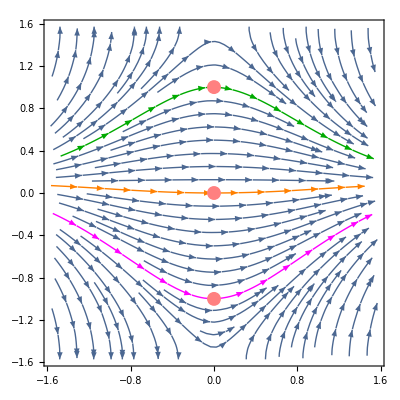

```mathematica
With[{func=x Exp[0.1y]Cos[y]},
Print[Grad[func,{x,y}]];StreamPlot[Evaluate@Grad[func,{x,y}],{x,-Pi/2,Pi/2},{y,-Pi/2,Pi/2},
StreamColorFunction->None,
StreamPoints->{{{{0,-1},Magenta},{{0,0},Orange},{{0,1},Darker[Green]},Automatic}},
Epilog->{ 
Pink,PointSize[0.025],Point/@{{0,-1},{0,0},{0,1}}
}
]
]
```

#### Problem 2

```mathematica
Probability[Z>0,Z\[Distributed]TransformedDistribution[X-Y,{X\[Distributed]NormalDistribution[10,1],Y\[Distributed]NormalDistribution[11,2]}
]
]
%//N
```

1/2 (1-Erf[1/(√10)])

0.32736

```mathematica
Solve[Evaluate[a+b(#1+1)+c(#1+1)#1==#2&@@@{{-1,1},{0,0},{1,1}}],{a,b,c}]
```

{{a→1,b→-1,c→1}}

```mathematica
Evaluate[a+b(#1+1)+c(#1+1)#1==#2&@@@{{-1,1},{0,0},{1,1}}]
```

{a==1,a+b==0,a+2 b+2 c==1}

```mathematica
A={{1,1,1},{0,1,3}}
```

{{1,1,1},{0,1,3}}

```mathematica
Transpose@A//MatrixForm
```

(1 | 0
1 | 1
1 | 3)

```mathematica
A.Transpose@A
```

{{3,4},{4,10}}

```mathematica
b={1,2,3}
```

{1,2,3}

```mathematica
A.b
```

{6,11}

```mathematica
(Transpose@A).{{1},{2},{3}}
```

Dot::dotsh: 张量 {{1,0},{1,1},{1,3}} 和 {{1},{2},{3}} 含有不兼容形状.

{{1,0},{1,1},{1,3}}.{{1},{2},{3}}

```mathematica
LinearSolve[A.Transpose@A,A.b]
```

{8/7,9/14}

```mathematica
Eigensystem[{{3,-1},{1,3}}]
```

{{3+ⅈ,3-ⅈ},{{ⅈ,1},{-ⅈ,1}}}

```mathematica
LinearSolve[]
```

```mathematica
{{3,-1},{1,3}}.{I,1}
```

{-1+3 ⅈ,3+ⅈ}

```mathematica
Eigenvectors[{{3,-1},{1,3}}]
```

{{ⅈ,1},{-ⅈ,1}}

```mathematica
(-1+3I)/(3+I)==I
```

True

```mathematica
Inverse[{{I,-I},{1,1}}]//MatrixForm
```

(-ⅈ/2 | 1/2
ⅈ/2 | 1/2)

```mathematica
P={{I,-I},{1,1}};
AA={{a1,0},{0,a2}};
```

```mathematica
P.AA.Inverse[P]//MatrixForm
```

(a1/2+a2/2 | (ⅈ a1)/2-(ⅈ a2)/2
-(ⅈ a1)/2+(ⅈ a2)/2 | a1/2+a2/2)

```mathematica
Solve[{2a b==1,a^2-b^2==3},{a,b}]//FullSimplify
```

{{a→-√(3/2+√(5/2)),b→-√(-3/2+√(5/2))},{a→√(3/2+√(5/2)),b→√(-3/2+√(5/2))},{a→Root-0.285 ⅈRoot[-1-12 #1^2+4 #1^4&,3]0.,b→ⅈ √(3/2+√(5/2))},{a→ⅈ √(-3/2+√(5/2)),b→Root-1.76 ⅈRoot[-1+12 #1^2+4 #1^4&,3]0.}}

```mathematica
Clear[a,b]
```

```mathematica
Eigenvalues[{{0,1,0,0},{3,0,-1,0},{0,0,0,1},{1,0,3,0}}]
```

{-√(3-ⅈ),-√(3+ⅈ),√(3+ⅈ),√(3-ⅈ)}

```mathematica
DSolve[{x''[t]-3x[t]+y[t]==0,y''[t]-x[t]-3y[t]==0},{x[t],y[t]},t]//FullSimplify
```

{{x[t]→1/4 (C[1] RootSum[10-6 #1^2+#1^4&,ⅇ^(t #1)&]+C[2] RootSum[10-6 #1^2+#1^4&,ⅇ^(t #1)/#1&]-C[3] RootSum[10-6 #1^2+#1^4&,ⅇ^(t #1)/(-3+#1^2)&]-C[4] RootSum[10-6 #1^2+#1^4&,ⅇ^(t #1)/(-3 #1+#1^3)&]),y[t]→1/4 (C[3] RootSum[10-6 #1^2+#1^4&,ⅇ^(t #1)&]+C[4] RootSum[10-6 #1^2+#1^4&,ⅇ^(t #1)/#1&]+C[1] RootSum[10-6 #1^2+#1^4&,ⅇ^(t #1)/(-3+#1^2)&]+C[2] RootSum[10-6 #1^2+#1^4&,ⅇ^(t #1)/(-3 #1+#1^3)&])}}

```mathematica
Solve[m^4-6m^2+10m==0,m]
```

{{m→0},{m→Root-3.05Root[10-6 #1+#1^3&,1]-3.0466803241500284},{m→Root1.52-0.981 ⅈRoot[10-6 #1+#1^3&,2]1.5233401620750142},{m→Root1.52+0.981 ⅈRoot[10-6 #1+#1^3&,3]1.5233401620750142}}

```mathematica
Integrate[8Pi h √(r^2-y^2),{y,0,r}]//FullSimplify
```

2 h π^2 r √(r^2)

```mathematica
A={{3/4,1/4,0,0},{1/4,1/2,1/4,0},{0,1/4,1/2,1/4},{0,0,1/4,3/4}}
Eigensystem@A
```

{{3/4,1/4,0,0},{1/4,1/2,1/4,0},{0,1/4,1/2,1/4},{0,0,1/4,3/4}}

{{1,1/4 (2+√2),1/2,1/4 (2-√2)},{{1,1,1,1},{-1,1-√2,-1+√2,1},{1,-1,-1,1},{-1,1+√2,-1-√2,1}}}

```mathematica
A-IdentityMatrix[3]//Ma
```

{{1/3,1/4,0},{1/4,-1/2,1/4},{0,1/4,-1/4}}

```mathematica
P={{0,0,0,0,1},{1,0,0,0,0},{1/2,1/2,0,0,0},{1/3,1/3,1/3,0,0},{1/4,1/4,1/4,1/4,0}}
```

{{0,0,0,0,1},{1,0,0,0,0},{1/2,1/2,0,0,0},{1/3,1/3,1/3,0,0},{1/4,1/4,1/4,1/4,0}}

```mathematica
Eigenvectors[Transpose@P]
```

{{1,1/2,1/3,1/4,1},{Root-0.193+0.612 ⅈRoot[1+7 #1+18 #1^2+24 #1^3+24 #1^4&,4]-0.19326174705001214,Root-0.406+0.0150 ⅈRoot[1-6 #1+168 #1^3+288 #1^4&,2]-0.40630555699692045,Root-0.283-0.255 ⅈRoot[1+6 #1+36 #1^2+96 #1^3+144 #1^4&,1]-0.28306562775128963,Root-0.117-0.372 ⅈRoot[3+12 #1+36 #1^2+56 #1^3+32 #1^4&,3]-0.11736706820177777,1},{Root-0.193-0.612 ⅈRoot[1+7 #1+18 #1^2+24 #1^3+24 #1^4&,3]-0.19326174705001214,Root-0.406-0.0150 ⅈRoot[1-6 #1+168 #1^3+288 #1^4&,1]-0.40630555699692045,Root-0.283+0.255 ⅈRoot[1+6 #1+36 #1^2+96 #1^3+144 #1^4&,2]-0.28306562775128963,Root-0.117+0.372 ⅈRoot[3+12 #1+36 #1^2+56 #1^3+32 #1^4&,4]-0.11736706820177777,1},{Root-0.307+0.0844 ⅈRoot[1+7 #1+18 #1^2+24 #1^3+24 #1^4&,2]-0.30673825294998786,Root0.115-0.0887 ⅈRoot[1-6 #1+168 #1^3+288 #1^4&,3]0.11463889033025378,Root-0.0503+0.213 ⅈRoot[1+6 #1+36 #1^2+96 #1^3+144 #1^4&,4]-0.05026770558204368,Root-0.758-0.209 ⅈRoot[3+12 #1+36 #1^2+56 #1^3+32 #1^4&,1]-0.7576329317982222,1},{Root-0.307-0.0844 ⅈRoot[1+7 #1+18 #1^2+24 #1^3+24 #1^4&,1]-0.30673825294998786,Root0.115+0.0887 ⅈRoot[1-6 #1+168 #1^3+288 #1^4&,4]0.11463889033025378,Root-0.0503-0.213 ⅈRoot[1+6 #1+36 #1^2+96 #1^3+144 #1^4&,3]-0.05026770558204368,Root-0.758+0.209 ⅈRoot[3+12 #1+36 #1^2+56 #1^3+32 #1^4&,2]-0.7576329317982222,1}}

```mathematica
Total[%[[1,;;]]]
```

37/12

```mathematica
Total[{1,1/2,1/3,1/4,1}]
```

37/12

```mathematica
MatrixPower[{{4/10,6/10},{1/10,9/10}},4]~N~10
```

{{0.1498,0.8502},{0.1417,0.8583}}

```mathematica
Integrate[Dot[{3(t/Pi+3/4)(Cos[t]/(√2)+1/2)^2,(t/Pi+3/4)^2,(Cos[t]/(√2)+1/2)^3+2(Sin[t]/(√2)+1/2)(t/Pi+3/4)},{-Sin[t]/√2,Cos[t]/√2,1/Pi}],{t,-3Pi/4,Pi/4}]
```

2

```mathematica
{{-3,4},{1,-3}}-m IdentityMatrix[2]
```

{{-3-m,4},{1,-3-m}}

```mathematica
Det@%
```

5+6 m+m^2

```mathematica
Eigenvectors[{{-3,4},{1,-3}}]
```

{{-2,1},{2,1}}

```mathematica
Eigensystem[{{-3,4},{1,-3}}]
```

{{-5,-1},{{-2,1},{2,1}}}

```mathematica
StreamPlot
```

```mathematica
{{-3,4},{1,-3}}.{x,y}
```

{-3 x+4 y,x-3 y}

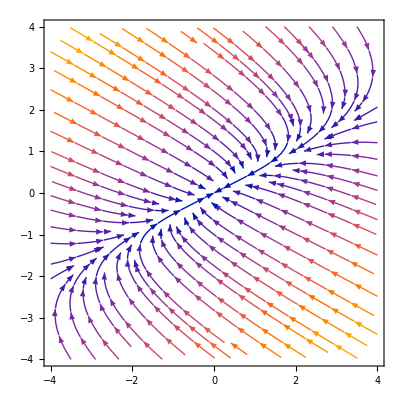

```mathematica
StreamPlot[%,{x,-4,4},{y,-4,4}]
```

```mathematica
Integrate[Pi-t,{t,0,Pi}]
```

π^2/2

```mathematica
g[t_]:=Piecewise[{{Pi/2,t<=0},{Pi-t,t>0}}]
```

```mathematica
g[1]
```

-1+π

```mathematica
Integrate[g[x]Sin[n x],{x,-Pi,Pi}]
```

(n π+n π Cos[n π]-2 Sin[n π])/(2 n^2)

```mathematica
Integrate[g[x]Cos[n x],x]
```

Piecewise[{{(π Sin[n x])/(2 n), x≤0}, {1/n^2-Cos[n x]/n^2+(π Sin[n x])/n-(x Sin[n x])/n, True}}]

```mathematica
Sum[1/(2n+1)^2,{n,0,+Infinity}]
```

π^2/8

```mathematica
g[t_]:=Piecewise[{{Cosh[t],0<=t<1},{-Cosh[1],1<=t<2}}]
```

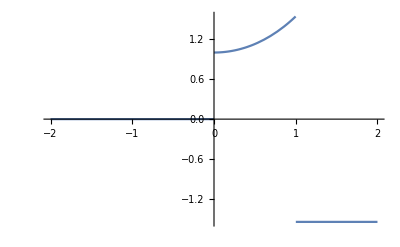

```mathematica
Plot[g[t],{t,-2,2}]
```

```mathematica
Cosh[1]//N
```

1.54308

```mathematica
D[Log[x+1],{x,4}]
```

-6/(1+x)^4

```mathematica
6/0.9^4/4*0.1^4
```

0.000228624

```mathematica
Integrate[(t-Pi)^n Exp[-s t],{t,Pi,s},Assumptions->n∈PositiveIntegers]//FullSimplify
```

(ⅇ^(-π s) (-π+s)^n (s (-π+s))^-n (Gamma[1+n]-Gamma[1+n,s (-π+s)]))/s

```mathematica
LaplaceTransform[Integrate[DiracDelta[m-Pi](t-m)^n,{m,0,t},Assumptions->t>0&&n∈PositiveIntegers],t,s]
```

ⅇ^(-π s) s^(-1-n) Gamma[1+n]

```mathematica
Integrate[DiracDelta[m-Pi](t-m)^n,{m,0,t},Assumptions->t>0&&n∈PositiveIntegers]
```

(-π+t)^n HeavisideTheta[-π+t]

```mathematica
InverseLaplaceTransform[Exp[-Pi s]/((s+1)^2+4),s,t]
```

```mathematica
-1/4 ⅈ ⅇ^(π-(1+2 ⅈ) t) (-1+ⅇ^(4 ⅈ t)) HeavisideTheta[-π+t]//Expand
```

```mathematica
1/4 ⅈ ⅇ^(π-(1+2 ⅈ) t) HeavisideTheta[-π+t]-1/4 ⅈ ⅇ^(π-(1-2 ⅈ) t) HeavisideTheta[-π+t]
```

1/4 ⅈ ⅇ^(π-(1+2 ⅈ) t) HeavisideTheta[-π+t]-1/4 ⅈ ⅇ^(π-(1-2 ⅈ) t) HeavisideTheta[-π+t]

```mathematica
ExpToTrig[1/4 ⅈ ⅇ^(π-(1+2 ⅈ) t) HeavisideTheta[-π+t]-1/4 ⅈ ⅇ^(π-(1-2 ⅈ) t) HeavisideTheta[-π+t]]
```

1/4 ⅈ Cosh[π-(1+2 ⅈ) t] HeavisideTheta[-π+t]-1/4 ⅈ Cosh[π-(1-2 ⅈ) t] HeavisideTheta[-π+t]+1/4 ⅈ HeavisideTheta[-π+t] Sinh[π-(1+2 ⅈ) t]-1/4 ⅈ HeavisideTheta[-π+t] Sinh[π-(1-2 ⅈ) t]

```mathematica
LaplaceTransform[1,t,s]
```

1/s

```mathematica
LaplaceTransform[Integrate[DiracDelta[m-Pi],{m,0,t}],t,s]
```

ⅇ^(-π s)/s

```mathematica
LaplaceTransform[ f''[t]+2f'[t]+2f[t],t,s]//FullSimplify
```

-((2+s) f[0])+(2+s (2+s)) LaplaceTransform[f[t],t,s]-f'[0]

```mathematica
LaplaceTransform[0,t,s]
```

0

```mathematica
InverseLaplaceTransform[1/((s+1)^2+1),s,t]
```

-1/2 ⅈ ⅇ^((-1-ⅈ) t) (-1+ⅇ^(2 ⅈ t))

```mathematica
x[t_]:=Exp[-t]Sin[t]
```

```mathematica
D[x[t],t]+x[t]
```

ⅇ^-t Cos[t]

```mathematica
+x
```